# Characteristic Polynomial for Quadratic Hamiltonian

## Studying the boson Hamiltonian in terms of the roots of its characteristic polynomial

## Using Mathematica’s implementations Eigenvalues,CharacteristicPolynomial

### Symbolic Hamiltonian

```mathematica
matel[n_,m_]:=StringTemplate["h_(`` ``)"][n,m];
ham02[n_]:=Table[Table[matel[2(i-1),2(j-1)],{j,1,n}],{i,1,n}];
ham13[n_]:=Table[Table[matel[2i+1,2j+1],{j,0,n-1}],{i,0,n-1}];
```

```mathematica
ham02[2]//MatrixForm
```

(h_(0 0) | h_(0 2)
h_(2 0) | h_(2 2))

```mathematica
ham13[2]//MatrixForm
```

(h_(1 1) | h_(1 3)
h_(3 1) | h_(3 3))

### Characteristic equation

```mathematica
charEq[M_,l_]:=Det[M-l*IdentityMatrix[Length[M]]];
p[m_]:=charEq[m,λ];
(*Solutions for the characteristic polynomial*)
solutions[pol_]:=Solve[pol==0,λ];
(*print the characteristic polynomial*)
printer[h_,pol_]:=Print[StringTemplate["P_(``)(λ)="][Length[h]],pol];
sols[h_,pol_]:=Module[{id},Print["Characteristic Polynomial:"];printer[h,p[h]];Print["Solutions:"];Do[Print[StringTemplate["λ_(``)="][id],Values@solutions[pol][[id,1]]],{id,1,Length[solutions[pol]]}]];
(*calculate the characteristic polynomial*)
charPol[m_]:=CharacteristicPolynomial[numMat3,λ];
(*calculate the coefficients of the polynomial*)
coeffs[pol_]:=CoefficientList[pol,λ];
```

Example for n = 2

```mathematica
h2=ham02[2];
p2=p[h2];
```

```mathematica
sols[h2,p2]
```

Characteristic Polynomial:

P_2(λ)=-h_(0 2) h_(2 0)+h_(0 0) h_(2 2)-h_(0 0) λ-h_(2 2) λ+λ^2

Solutions:

λ_1=1/2 (h_(0 0)+h_(2 2)-√((h_(0 0))^2+4 h_(0 2) h_(2 0)-2 h_(0 0) h_(2 2)+(h_(2 2))^2))

λ_2=1/2 (h_(0 0)+h_(2 2)+√((h_(0 0))^2+4 h_(0 2) h_(2 0)-2 h_(0 0) h_(2 2)+(h_(2 2))^2))

Example for n = 4

```mathematica
h3=ham02[3];
p3=p[h3];
```

```mathematica
sols[h3,p3]
```

Characteristic Polynomial:

P_3(λ)=-h_(0 4) h_(2 2) h_(4 0)+h_(0 2) h_(2 4) h_(4 0)+h_(0 4) h_(2 0) h_(4 2)-h_(0 0) h_(2 4) h_(4 2)-h_(0 2) h_(2 0) h_(4 4)+h_(0 0) h_(2 2) h_(4 4)+h_(0 2) h_(2 0) λ-h_(0 0) h_(2 2) λ+h_(0 4) h_(4 0) λ+h_(2 4) h_(4 2) λ-h_(0 0) h_(4 4) λ-h_(2 2) h_(4 4) λ+h_(0 0) λ^2+h_(2 2) λ^2+h_(4 4) λ^2-λ^3

Solutions:

λ_1=1/3 (h_(0 0)+h_(2 2)+h_(4 4))+(2^(1/3) (-(h_(0 0)+h_(2 2)+h_(4 4))^2-3 (h_(0 2) h_(2 0)-h_(0 0) h_(2 2)+h_(0 4) h_(4 0)+h_(2 4) h_(4 2)-h_(0 0) h_(4 4)-h_(2 2) h_(4 4))))/(3 (-2 (h_(0 0))^3-9 h_(0 0) h_(0 2) h_(2 0)+3 (h_(0 0))^2 h_(2 2)-9 h_(0 2) h_(2 0) h_(2 2)+3 h_(0 0) (h_(2 2))^2-2 (h_(2 2))^3-9 h_(0 0) h_(0 4) h_(4 0)+18 h_(0 4) h_(2 2) h_(4 0)-27 h_(0 2) h_(2 4) h_(4 0)-27 h_(0 4) h_(2 0) h_(4 2)+18 h_(0 0) h_(2 4) h_(4 2)-9 h_(2 2) h_(2 4) h_(4 2)+3 (h_(0 0))^2 h_(4 4)+18 h_(0 2) h_(2 0) h_(4 4)-12 h_(0 0) h_(2 2) h_(4 4)+3 (h_(2 2))^2 h_(4 4)-9 h_(0 4) h_(4 0) h_(4 4)-9 h_(2 4) h_(4 2) h_(4 4)+3 h_(0 0) (h_(4 4))^2+3 h_(2 2) (h_(4 4))^2-2 (h_(4 4))^3+√((-2 (h_(0 0))^3-9 h_(0 0) h_(0 2) h_(2 0)+3 (h_(0 0))^2 h_(2 2)-9 h_(0 2) h_(2 0) h_(2 2)+3 h_(0 0) (h_(2 2))^2-2 (h_(2 2))^3-9 h_(0 0) h_(0 4) h_(4 0)+18 h_(0 4) h_(2 2) h_(4 0)-27 h_(0 2) h_(2 4) h_(4 0)-27 h_(0 4) h_(2 0) h_(4 2)+18 h_(0 0) h_(2 4) h_(4 2)-9 h_(2 2) h_(2 4) h_(4 2)+3 (h_(0 0))^2 h_(4 4)+18 h_(0 2) h_(2 0) h_(4 4)-12 h_(0 0) h_(2 2) h_(4 4)+3 (h_(2 2))^2 h_(4 4)-9 h_(0 4) h_(4 0) h_(4 4)-9 h_(2 4) h_(4 2) h_(4 4)+3 h_(0 0) (h_(4 4))^2+3 h_(2 2) (h_(4 4))^2-2 (h_(4 4))^3)^2+4 (-(h_(0 0)+h_(2 2)+h_(4 4))^2-3 (h_(0 2) h_(2 0)-h_(0 0) h_(2 2)+h_(0 4) h_(4 0)+h_(2 4) h_(4 2)-h_(0 0) h_(4 4)-h_(2 2) h_(4 4)))^3))^(1/3))-1/(3 2^(1/3))(-2 (h_(0 0))^3-9 h_(0 0) h_(0 2) h_(2 0)+3 (h_(0 0))^2 h_(2 2)-9 h_(0 2) h_(2 0) h_(2 2)+3 h_(0 0) (h_(2 2))^2-2 (h_(2 2))^3-9 h_(0 0) h_(0 4) h_(4 0)+18 h_(0 4) h_(2 2) h_(4 0)-27 h_(0 2) h_(2 4) h_(4 0)-27 h_(0 4) h_(2 0) h_(4 2)+18 h_(0 0) h_(2 4) h_(4 2)-9 h_(2 2) h_(2 4) h_(4 2)+3 (h_(0 0))^2 h_(4 4)+18 h_(0 2) h_(2 0) h_(4 4)-12 h_(0 0) h_(2 2) h_(4 4)+3 (h_(2 2))^2 h_(4 4)-9 h_(0 4) h_(4 0) h_(4 4)-9 h_(2 4) h_(4 2) h_(4 4)+3 h_(0 0) (h_(4 4))^2+3 h_(2 2) (h_(4 4))^2-2 (h_(4 4))^3+√((-2 (h_(0 0))^3-9 h_(0 0) h_(0 2) h_(2 0)+3 (h_(0 0))^2 h_(2 2)-9 h_(0 2) h_(2 0) h_(2 2)+3 h_(0 0) (h_(2 2))^2-2 (h_(2 2))^3-9 h_(0 0) h_(0 4) h_(4 0)+18 h_(0 4) h_(2 2) h_(4 0)-27 h_(0 2) h_(2 4) h_(4 0)-27 h_(0 4) h_(2 0) h_(4 2)+18 h_(0 0) h_(2 4) h_(4 2)-9 h_(2 2) h_(2 4) h_(4 2)+3 (h_(0 0))^2 h_(4 4)+18 h_(0 2) h_(2 0) h_(4 4)-12 h_(0 0) h_(2 2) h_(4 4)+3 (h_(2 2))^2 h_(4 4)-9 h_(0 4) h_(4 0) h_(4 4)-9 h_(2 4) h_(4 2) h_(4 4)+3 h_(0 0) (h_(4 4))^2+3 h_(2 2) (h_(4 4))^2-2 (h_(4 4))^3)^2+4 (-(h_(0 0)+h_(2 2)+h_(4 4))^2-3 (h_(0 2) h_(2 0)-h_(0 0) h_(2 2)+h_(0 4) h_(4 0)+h_(2 4) h_(4 2)-h_(0 0) h_(4 4)-h_(2 2) h_(4 4)))^3))^(1/3)

λ_2=1/3 (h_(0 0)+h_(2 2)+h_(4 4))-((1+ⅈ √3) (-(h_(0 0)+h_(2 2)+h_(4 4))^2-3 (h_(0 2) h_(2 0)-h_(0 0) h_(2 2)+h_(0 4) h_(4 0)+h_(2 4) h_(4 2)-h_(0 0) h_(4 4)-h_(2 2) h_(4 4))))/(3 2^(2/3) (-2 (h_(0 0))^3-9 h_(0 0) h_(0 2) h_(2 0)+3 (h_(0 0))^2 h_(2 2)-9 h_(0 2) h_(2 0) h_(2 2)+3 h_(0 0) (h_(2 2))^2-2 (h_(2 2))^3-9 h_(0 0) h_(0 4) h_(4 0)+18 h_(0 4) h_(2 2) h_(4 0)-27 h_(0 2) h_(2 4) h_(4 0)-27 h_(0 4) h_(2 0) h_(4 2)+18 h_(0 0) h_(2 4) h_(4 2)-9 h_(2 2) h_(2 4) h_(4 2)+3 (h_(0 0))^2 h_(4 4)+18 h_(0 2) h_(2 0) h_(4 4)-12 h_(0 0) h_(2 2) h_(4 4)+3 (h_(2 2))^2 h_(4 4)-9 h_(0 4) h_(4 0) h_(4 4)-9 h_(2 4) h_(4 2) h_(4 4)+3 h_(0 0) (h_(4 4))^2+3 h_(2 2) (h_(4 4))^2-2 (h_(4 4))^3+√((-2 (h_(0 0))^3-9 h_(0 0) h_(0 2) h_(2 0)+3 (h_(0 0))^2 h_(2 2)-9 h_(0 2) h_(2 0) h_(2 2)+3 h_(0 0) (h_(2 2))^2-2 (h_(2 2))^3-9 h_(0 0) h_(0 4) h_(4 0)+18 h_(0 4) h_(2 2) h_(4 0)-27 h_(0 2) h_(2 4) h_(4 0)-27 h_(0 4) h_(2 0) h_(4 2)+18 h_(0 0) h_(2 4) h_(4 2)-9 h_(2 2) h_(2 4) h_(4 2)+3 (h_(0 0))^2 h_(4 4)+18 h_(0 2) h_(2 0) h_(4 4)-12 h_(0 0) h_(2 2) h_(4 4)+3 (h_(2 2))^2 h_(4 4)-9 h_(0 4) h_(4 0) h_(4 4)-9 h_(2 4) h_(4 2) h_(4 4)+3 h_(0 0) (h_(4 4))^2+3 h_(2 2) (h_(4 4))^2-2 (h_(4 4))^3)^2+4 (-(h_(0 0)+h_(2 2)+h_(4 4))^2-3 (h_(0 2) h_(2 0)-h_(0 0) h_(2 2)+h_(0 4) h_(4 0)+h_(2 4) h_(4 2)-h_(0 0) h_(4 4)-h_(2 2) h_(4 4)))^3))^(1/3))+1/(6 2^(1/3))(1-ⅈ √3) (-2 (h_(0 0))^3-9 h_(0 0) h_(0 2) h_(2 0)+3 (h_(0 0))^2 h_(2 2)-9 h_(0 2) h_(2 0) h_(2 2)+3 h_(0 0) (h_(2 2))^2-2 (h_(2 2))^3-9 h_(0 0) h_(0 4) h_(4 0)+18 h_(0 4) h_(2 2) h_(4 0)-27 h_(0 2) h_(2 4) h_(4 0)-27 h_(0 4) h_(2 0) h_(4 2)+18 h_(0 0) h_(2 4) h_(4 2)-9 h_(2 2) h_(2 4) h_(4 2)+3 (h_(0 0))^2 h_(4 4)+18 h_(0 2) h_(2 0) h_(4 4)-12 h_(0 0) h_(2 2) h_(4 4)+3 (h_(2 2))^2 h_(4 4)-9 h_(0 4) h_(4 0) h_(4 4)-9 h_(2 4) h_(4 2) h_(4 4)+3 h_(0 0) (h_(4 4))^2+3 h_(2 2) (h_(4 4))^2-2 (h_(4 4))^3+√((-2 (h_(0 0))^3-9 h_(0 0) h_(0 2) h_(2 0)+3 (h_(0 0))^2 h_(2 2)-9 h_(0 2) h_(2 0) h_(2 2)+3 h_(0 0) (h_(2 2))^2-2 (h_(2 2))^3-9 h_(0 0) h_(0 4) h_(4 0)+18 h_(0 4) h_(2 2) h_(4 0)-27 h_(0 2) h_(2 4) h_(4 0)-27 h_(0 4) h_(2 0) h_(4 2)+18 h_(0 0) h_(2 4) h_(4 2)-9 h_(2 2) h_(2 4) h_(4 2)+3 (h_(0 0))^2 h_(4 4)+18 h_(0 2) h_(2 0) h_(4 4)-12 h_(0 0) h_(2 2) h_(4 4)+3 (h_(2 2))^2 h_(4 4)-9 h_(0 4) h_(4 0) h_(4 4)-9 h_(2 4) h_(4 2) h_(4 4)+3 h_(0 0) (h_(4 4))^2+3 h_(2 2) (h_(4 4))^2-2 (h_(4 4))^3)^2+4 (-(h_(0 0)+h_(2 2)+h_(4 4))^2-3 (h_(0 2) h_(2 0)-h_(0 0) h_(2 2)+h_(0 4) h_(4 0)+h_(2 4) h_(4 2)-h_(0 0) h_(4 4)-h_(2 2) h_(4 4)))^3))^(1/3)

λ_3=1/3 (h_(0 0)+h_(2 2)+h_(4 4))-((1-ⅈ √3) (-(h_(0 0)+h_(2 2)+h_(4 4))^2-3 (h_(0 2) h_(2 0)-h_(0 0) h_(2 2)+h_(0 4) h_(4 0)+h_(2 4) h_(4 2)-h_(0 0) h_(4 4)-h_(2 2) h_(4 4))))/(3 2^(2/3) (-2 (h_(0 0))^3-9 h_(0 0) h_(0 2) h_(2 0)+3 (h_(0 0))^2 h_(2 2)-9 h_(0 2) h_(2 0) h_(2 2)+3 h_(0 0) (h_(2 2))^2-2 (h_(2 2))^3-9 h_(0 0) h_(0 4) h_(4 0)+18 h_(0 4) h_(2 2) h_(4 0)-27 h_(0 2) h_(2 4) h_(4 0)-27 h_(0 4) h_(2 0) h_(4 2)+18 h_(0 0) h_(2 4) h_(4 2)-9 h_(2 2) h_(2 4) h_(4 2)+3 (h_(0 0))^2 h_(4 4)+18 h_(0 2) h_(2 0) h_(4 4)-12 h_(0 0) h_(2 2) h_(4 4)+3 (h_(2 2))^2 h_(4 4)-9 h_(0 4) h_(4 0) h_(4 4)-9 h_(2 4) h_(4 2) h_(4 4)+3 h_(0 0) (h_(4 4))^2+3 h_(2 2) (h_(4 4))^2-2 (h_(4 4))^3+√((-2 (h_(0 0))^3-9 h_(0 0) h_(0 2) h_(2 0)+3 (h_(0 0))^2 h_(2 2)-9 h_(0 2) h_(2 0) h_(2 2)+3 h_(0 0) (h_(2 2))^2-2 (h_(2 2))^3-9 h_(0 0) h_(0 4) h_(4 0)+18 h_(0 4) h_(2 2) h_(4 0)-27 h_(0 2) h_(2 4) h_(4 0)-27 h_(0 4) h_(2 0) h_(4 2)+18 h_(0 0) h_(2 4) h_(4 2)-9 h_(2 2) h_(2 4) h_(4 2)+3 (h_(0 0))^2 h_(4 4)+18 h_(0 2) h_(2 0) h_(4 4)-12 h_(0 0) h_(2 2) h_(4 4)+3 (h_(2 2))^2 h_(4 4)-9 h_(0 4) h_(4 0) h_(4 4)-9 h_(2 4) h_(4 2) h_(4 4)+3 h_(0 0) (h_(4 4))^2+3 h_(2 2) (h_(4 4))^2-2 (h_(4 4))^3)^2+4 (-(h_(0 0)+h_(2 2)+h_(4 4))^2-3 (h_(0 2) h_(2 0)-h_(0 0) h_(2 2)+h_(0 4) h_(4 0)+h_(2 4) h_(4 2)-h_(0 0) h_(4 4)-h_(2 2) h_(4 4)))^3))^(1/3))+1/(6 2^(1/3))(1+ⅈ √3) (-2 (h_(0 0))^3-9 h_(0 0) h_(0 2) h_(2 0)+3 (h_(0 0))^2 h_(2 2)-9 h_(0 2) h_(2 0) h_(2 2)+3 h_(0 0) (h_(2 2))^2-2 (h_(2 2))^3-9 h_(0 0) h_(0 4) h_(4 0)+18 h_(0 4) h_(2 2) h_(4 0)-27 h_(0 2) h_(2 4) h_(4 0)-27 h_(0 4) h_(2 0) h_(4 2)+18 h_(0 0) h_(2 4) h_(4 2)-9 h_(2 2) h_(2 4) h_(4 2)+3 (h_(0 0))^2 h_(4 4)+18 h_(0 2) h_(2 0) h_(4 4)-12 h_(0 0) h_(2 2) h_(4 4)+3 (h_(2 2))^2 h_(4 4)-9 h_(0 4) h_(4 0) h_(4 4)-9 h_(2 4) h_(4 2) h_(4 4)+3 h_(0 0) (h_(4 4))^2+3 h_(2 2) (h_(4 4))^2-2 (h_(4 4))^3+√((-2 (h_(0 0))^3-9 h_(0 0) h_(0 2) h_(2 0)+3 (h_(0 0))^2 h_(2 2)-9 h_(0 2) h_(2 0) h_(2 2)+3 h_(0 0) (h_(2 2))^2-2 (h_(2 2))^3-9 h_(0 0) h_(0 4) h_(4 0)+18 h_(0 4) h_(2 2) h_(4 0)-27 h_(0 2) h_(2 4) h_(4 0)-27 h_(0 4) h_(2 0) h_(4 2)+18 h_(0 0) h_(2 4) h_(4 2)-9 h_(2 2) h_(2 4) h_(4 2)+3 (h_(0 0))^2 h_(4 4)+18 h_(0 2) h_(2 0) h_(4 4)-12 h_(0 0) h_(2 2) h_(4 4)+3 (h_(2 2))^2 h_(4 4)-9 h_(0 4) h_(4 0) h_(4 4)-9 h_(2 4) h_(4 2) h_(4 4)+3 h_(0 0) (h_(4 4))^2+3 h_(2 2) (h_(4 4))^2-2 (h_(4 4))^3)^2+4 (-(h_(0 0)+h_(2 2)+h_(4 4))^2-3 (h_(0 2) h_(2 0)-h_(0 0) h_(2 2)+h_(0 4) h_(4 0)+h_(2 4) h_(4 2)-h_(0 0) h_(4 4)-h_(2 2) h_(4 4)))^3))^(1/3)

### Numerical example for n=3

```mathematica
numMat3=({{1, 1, 1}, {1, 1/2, 1/3}, {1, 2, 3}});
p3num=p[numMat3];
(*Characteristic polynomial for the 3x3 matrix*)
sols[numMat3,p[numMat3]]
```

Characteristic Polynomial:

P_3(λ)=-1/3-(7 λ)/3+(9 λ^2)/2-λ^3

Solutions:

λ_1=Root-0.116Root[2+14 #1-27 #1^2+6 #1^3&,1]-0.11616199292700435

λ_2=Root0.740Root[2+14 #1-27 #1^2+6 #1^3&,2]0.7403814155072762

λ_3=Root3.88Root[2+14 #1-27 #1^2+6 #1^3&,3]3.8757805774197283

```mathematica
vieteRel[pol_]:=coeffs[pol][[Length[Solve[pol==0,λ]]+1]]*Product[λ-N[Values@Solve[pol==0,λ][[id,1]]],{id,1,Length[Solve[pol==0,λ]]}];
```

## Boson Hamiltonian up to N=2 order - H_3 (even case)

```mathematica
boson2=({{0, -√2 q}, {-√2 q, 2}});
```

```mathematica
p[boson2]
```

-2 q^2-2 λ+λ^2

```mathematica
vieteRel[p[boson2]]
```

(-1.-√(1.+2. q^2)+λ) (-1.+1. √(1.+2. q^2)+λ)

## Boson Hamiltonian up to N=3 order - H_3 (even case)

```mathematica
boson3=({{0, -√2 v, 0}, {-√2 v, 2 e, -2 √3 v}, {0, -2 √3 v, 4 e}});boson3=boson3/e;boson3=boson3/.v/e->q;
```

### Matrix form of H_3

```mathematica
boson3//MatrixForm
```

(0 | -√2 q | 0
-√2 q | 2 | -2 √3 q
0 | -2 √3 q | 4)

### Polynomial for of the Hamiltonian H_3

```mathematica
p[boson3]
```

-8 q^2-8 λ+14 q^2 λ+6 λ^2-λ^3

### Checking the evolution of λ’s with the q-ratio

```mathematica
checkSolutions[matrix_,ratio_]:=N[Solve[(p[boson3]/.{q->ratio})==0,λ]];
Manipulate[N[Im[Values@Solve[p[boson3]==0,λ]/.{q->proba}]],{proba,0,4}]
```

### The characteristic polynomial of H_3

```mathematica
sols[boson3,p[boson3]]
```

Characteristic Polynomial:

P_3(λ)=-8 q^2-8 λ+14 q^2 λ+6 λ^2-λ^3

Solutions:

λ_1=2+(-12-42 q^2)/(3 6^(1/3) (-45 q^2+√3 √(-16-168 q^2+87 q^4-686 q^6))^(1/3))-(2^(1/3) (-45 q^2+√3 √(-16-168 q^2+87 q^4-686 q^6))^(1/3))/3^(2/3)

λ_2=2-((1+ⅈ √3) (-12-42 q^2))/(6 6^(1/3) (-45 q^2+√3 √(-16-168 q^2+87 q^4-686 q^6))^(1/3))+((1-ⅈ √3) (-45 q^2+√3 √(-16-168 q^2+87 q^4-686 q^6))^(1/3))/6^(2/3)

λ_3=2-((1-ⅈ √3) (-12-42 q^2))/(6 6^(1/3) (-45 q^2+√3 √(-16-168 q^2+87 q^4-686 q^6))^(1/3))+((1+ⅈ √3) (-45 q^2+√3 √(-16-168 q^2+87 q^4-686 q^6))^(1/3))/6^(2/3)

### Coefficients of 𝒫_3(H_3;λ)

```mathematica
coeffs[p[boson3]]
```

{-8 q^2,-8+14 q^2,6,-1}

```mathematica
FullSimplify[N[vieteRel[p[boson3]]]/.{(-45. q^2+1.7320508075688772 √(-16.-168. q^2+87. q^4-686. q^6))->w,(0.09172020135818407-0.15886404883282274 ⅈ) (-12.-42. q^2)->t}]
```

```mathematica
-1. (-2.+t/w^(1/3)-(0.30285343213869+0.5245575317108241 ⅈ) w^(1/3)+λ) (-2.+((0.09172020135818407+0.15886404883282274 ⅈ) (-12.-42. q^2))/w^(1/3)-(0.30285343213869-0.5245575317108241 ⅈ) w^(1/3)+λ) (-2.+(2.2012848325964174+7.7044969140874615 q^2)/w^(1/3)+0.60570686427738 w^(1/3)+λ)
```

### Roots of polynomial

```mathematica
Det[boson3-λ IdentityMatrix[Length[boson3]]]
```

-8 q^2-8 λ+14 q^2 λ+6 λ^2-λ^3

```mathematica
Poly[λ_]:=-8 q^2-8 λ+14 q^2 λ+6 λ^2-λ^3;
```

```mathematica
Manipulate[Plot[Poly[x]/.{q->v},{x,0,10}],{v,0,3}]
```

## Boson Hamiltonian up to N=3 order - H_3 (odd case)

```mathematica
boson3Odd=({{e, -√6 v}, {-√6 v, 3 e}});boson3Odd=boson3Odd/e;boson3Odd=boson3Odd/.{v/e->q};
```

```mathematica
boson3Odd//MatrixForm
```

(1 | -√6 q
-√6 q | 3)

```mathematica
sols[boson3Odd,p[boson3Odd]]
```

Characteristic Polynomial:

P_2(λ)=3-6 q^2-4 λ+λ^2

Solutions:

λ_1=2-√(1+6 q^2)

λ_2=2+√(1+6 q^2)

```mathematica
vieteRel[p[boson3Odd]]
```

(-2.-√(1.+6. q^2)+λ) (-2.+1. √(1.+6. q^2)+λ)

```mathematica
coeffs[p[boson3Odd]]
```

{3-6 q^2,-4,1}

## Matrix elements of H_n^b

```mathematica
matEl[n_,m_,e_,v_]:=Piecewise[{{e*m, n==m}, {Sqrt[m+1]Sqrt[m+2](-v), n-m==2}, {Sqrt[m]Sqrt[m-1](-v), n-m==-2}}];
HBoson[n_,e_,v_,parity_]:=Piecewise[{{Table[Table[matEl[2(i-1),2(j-1),e,v],{j,1,n}],{i,1,n}], parity==0}, {Table[Table[matEl[2i+1,2j+1,e,v],{j,0,n-1}],{i,0,n-1}], parity==1}}];
```

```mathematica
HBoson[4,e,v,0]//MatrixForm
```

(0 | -√2 v | 0 | 0
-√2 v | 2 e | -2 √3 v | 0
0 | -2 √3 v | 4 e | -√30 v
0 | 0 | -√30 v | 6 e)

```mathematica
HBoson[4,e,v,1]//MatrixForm
```

(e | -√6 v | 0 | 0
-√6 v | 3 e | -2 √5 v | 0
0 | -2 √5 v | 5 e | -√42 v
0 | 0 | -√42 v | 7 e)

## Boson Hamiltonian N=10 order - analytic approach

### Even Case: 0,2,4

```mathematica
boson10=HBoson[10,1,q,0];
```

```mathematica
Do[Print[(N[Eigenvalues[boson10]/.{q->1}])[[id]]],{id,1,Length[Eigenvalues[boson10]/.{q->1}]}]
```

-11.6496

-5.83432

-2.09878

-0.170188

2.40978

6.55402

12.0478

19.1292

28.3619

41.2502

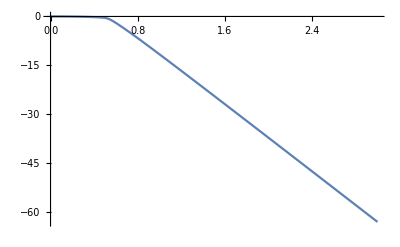

```mathematica
Plot[(N[Eigenvalues[boson10]/.{q->u}])[[1]],{u,0,3}]
```

## Evolution of λ with the q-ratio